```mathematica
FullSimplify[Series[Log[1 - ((b-a) / a) * x],{x,0,  15}]]
```

(1-b/a) x-((a-b)^2 x^2)/(2 a^2)+((a-b)^3 x^3)/(3 a^3)-((a-b)^4 x^4)/(4 a^4)+((a-b)^5 x^5)/(5 a^5)-((a-b)^6 x^6)/(6 a^6)+((a-b)^7 x^7)/(7 a^7)-((a-b)^8 x^8)/(8 a^8)+((a-b)^9 x^9)/(9 a^9)-((a-b)^10 x^10)/(10 a^10)+((a-b)^11 x^11)/(11 a^11)-((a-b)^12 x^12)/(12 a^12)+((a-b)^13 x^13)/(13 a^13)-((a-b)^14 x^14)/(14 a^14)+((a-b)^15 x^15)/(15 a^15)+O[x]^16

```mathematica
f[x_, a_,b_]=(1-b/a) x-((a-b)^2 x^2)/(2 a^2)+((a-b)^3 x^3)/(3 a^3)-((a-b)^4 x^4)/(4 a^4)+((a-b)^5 x^5)/(5 a^5)-((a-b)^6 x^6)/(6 a^6)+((a-b)^7 x^7)/(7 a^7)-((a-b)^8 x^8)/(8 a^8)+((a-b)^9 x^9)/(9 a^9)-((a-b)^10 x^10)/(10 a^10)+((a-b)^11 x^11)/(11 a^11)-((a-b)^12 x^12)/(12 a^12)+((a-b)^13 x^13)/(13 a^13)-((a-b)^14 x^14)/(14 a^14)+((a-b)^15 x^15)/(15 a^15)
```

(1-b/a) x-((a-b)^2 x^2)/(2 a^2)+((a-b)^3 x^3)/(3 a^3)-((a-b)^4 x^4)/(4 a^4)+((a-b)^5 x^5)/(5 a^5)-((a-b)^6 x^6)/(6 a^6)+((a-b)^7 x^7)/(7 a^7)-((a-b)^8 x^8)/(8 a^8)+((a-b)^9 x^9)/(9 a^9)-((a-b)^10 x^10)/(10 a^10)+((a-b)^11 x^11)/(11 a^11)-((a-b)^12 x^12)/(12 a^12)+((a-b)^13 x^13)/(13 a^13)-((a-b)^14 x^14)/(14 a^14)+((a-b)^15 x^15)/(15 a^15)

```mathematica
g[x_] = f[x, 6.0, 7.0]- Log[1 - ((7 - 6) / 6)*x]
```

-0.166667 x-0.0138889 x^2-0.00154321 x^3-0.000192901 x^4-0.0000257202 x^5-3.57225×10^-6 x^6-5.10321×10^-7 x^7-7.44218×10^-8 x^8-1.10254×10^-8 x^9-1.65382×10^-9 x^10-2.50578×10^-10 x^11-3.82828×10^-11 x^12-5.88966×10^-12 x^13-9.11495×10^-13 x^14-1.41788×10^-13 x^15-Log[1-x/6]

```mathematica
g[1.0]
```

2.63956×10^-14

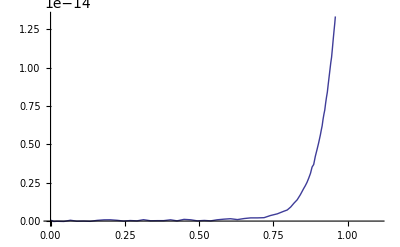

```mathematica
Plot[{f[x, 6.0, 7.0]- Log[1 - ((7 - 6) / 6)*x]}, {x, 0, 1.1}]
```

```mathematica
Series[Log[x], {x, a, 10}]
```

Log[a]+(x-a)/a-(x-a)^2/(2 a^2)+(x-a)^3/(3 a^3)-(x-a)^4/(4 a^4)+(x-a)^5/(5 a^5)-(x-a)^6/(6 a^6)+(x-a)^7/(7 a^7)-(x-a)^8/(8 a^8)+(x-a)^9/(9 a^9)-(x-a)^10/(10 a^10)+O[x-a]^11